```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],Background->White]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/D"];
```

```mathematica
data=Import[#,"Table"]&/@FileNames["eval*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
```

```mathematica
Do[ReEv[i]=Table[vec[i][[j,1]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv[i]=Max[ReEv[i]],{i,1,Length[data]}]
```

```mathematica
xs=Table[i*2/100,{i,1,Length[data]}];
ys=Table[2^(3/2)MaxEv[i],{i,1,Length[data]}];
pairs=Thread[{xs,ys}];
```

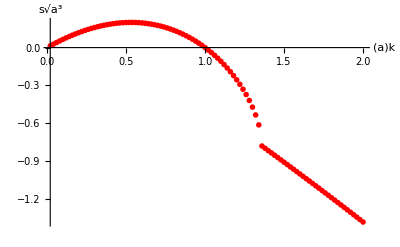

```mathematica
l1=ListPlot[pairs,PlotRange->All,Joined->False,PlotStyle->{PointSize[0.01],Red},AxesLabel->{"(a)k","s√(a^3)"},LabelStyle->Directive[14]]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_Spectral/V"]
```

/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/V

```mathematica
(* ClearAll["Global`*"]
```

```mathematica
(* data=Import[#,"Table"]&/@FileNames["x.*"];
```

```mathematica
(* Table[vec[j]=data[[j]],{j,1,Length[data]}];
Table[realvec[i]=Table[vec[i][[j,1]],{j,1,3Length[data]}],{i,1,Length[data]}];
Table[imvec[i]=Table[vec[i][[j,2]],{j,1,3Length[data]}],{i,1,Length[data]}];
```

```mathematica
(* only first two have true nonzero eigenvalues *)
```

```mathematica
(* Table[ListPlot[realvec[j],PlotRange->All,Joined->True],{j,1,Length[data]}];
```

```mathematica
gamm=1;
aa=2;
rhoo=1;
muu=0.5;
```

```mathematica
(* (gamm(1-(k*aa)^2))/(rhoo*aa^3)(k*aa)/n(I*n*rhoo)/(muu(k^2+(I*n*rhoo)/muu+k^2))(D[BesselJ[0,x],x]/.x->(I*k*aa))+2*k^2*muu/rhoo((D[D[BesselJ[0,x],x],x]/.x->(I*k*aa))-(2k*Sqrt[k^2+(I*n*rhoo)/muu])/(k^2+(I*n*rhoo)/muu+k^2)(D[BesselJ[0,x],x]/.x->(I*k*aa))/(D[BesselJ[0,x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))(D[D[BesselJ[0,x],x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))-Sqrt[k^2+(I*n*rhoo)/muu]/k(I*n*rhoo)/(muu(k^2+(I*n*rhoo)/muu+k^2))(D[BesselJ[0,x],x]/.x->(I*k*aa))/(D[BesselJ[0,x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))(BesselJ[0,x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa)))-n/(k*aa)(I*k*aa*(BesselJ[0,x]/.x->(I*k*aa))-(2*k^2)/(k^2+(I*n*rhoo)/muu+k^2)(D[BesselJ[0,x],x]/.x->(I*k*aa))/(D[BesselJ[0,x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))I*Sqrt[k^2+(I*n*rhoo)/muu]*aa*(BesselJ[0,x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))) *)
```

```mathematica
sol=Table[FindRoot[(gamm(1-(k*aa)^2))/(rhoo*aa^3)(k*aa)/n(I*n*rhoo)/(muu(k^2+(I*n*rhoo)/muu+k^2))(D[BesselJ[0,x],x]/.x->(I*k*aa))+2*k^2*muu/rhoo((D[D[BesselJ[0,x],x],x]/.x->(I*k*aa))-(2*k*Sqrt[k^2+(I*n*rhoo)/muu])/(k^2+(I*n*rhoo)/muu+k^2)(D[BesselJ[0,x],x]/.x->(I*k*aa))/(D[BesselJ[0,x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))(D[D[BesselJ[0,x],x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))-Sqrt[k^2+(I*n*rhoo)/muu]/k(I*n*rhoo)/(muu(k^2+(I*n*rhoo)/muu+k^2))(D[BesselJ[0,x],x]/.x->(I*k*aa))/(D[BesselJ[0,x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))(BesselJ[0,x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa)))-n/(k*aa)(I*k*aa*(BesselJ[0,x]/.x->(I*k*aa))-(2*k^2)/(k^2+(I*n*rhoo)/muu+k^2)(D[BesselJ[0,x],x]/.x->(I*k*aa))/(D[BesselJ[0,x],x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))I*Sqrt[k^2+(I*n*rhoo)/muu]*aa*(BesselJ[0,x]/.x->(I*Sqrt[k^2+(I*n*rhoo)/muu]*aa))),{n,-1},MaxIterations->100000,AccuracyGoal->MachinePrecision,PrecisionGoal->MachinePrecision],{k,.01,1,.01}];
```

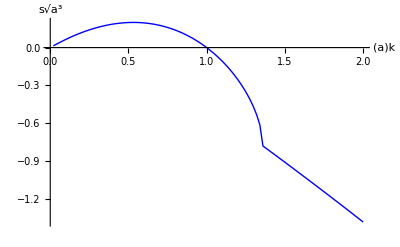

```mathematica
xs2=Table[i*2./100,{i,1,100}];
ys2=-Im[n/.sol]*2^(3/2);
pairs3=Thread[{xs2,ys2}];
l5=ListPlot[pairs3,Joined->True,PlotStyle->Blue,Frame->False,AxesLabel->{"(a)k","s√(a^3)"},LabelStyle->Directive[14]]
```

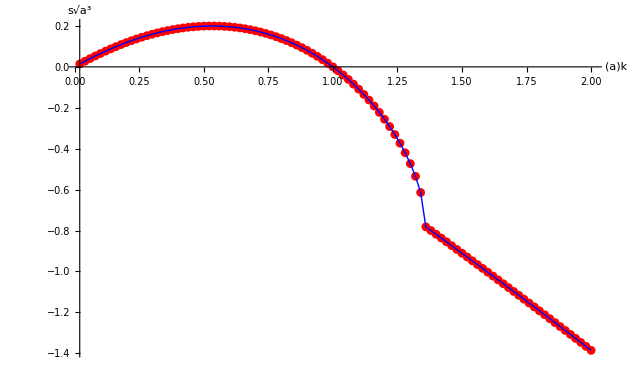

```mathematica
Show[l1,l5]
```

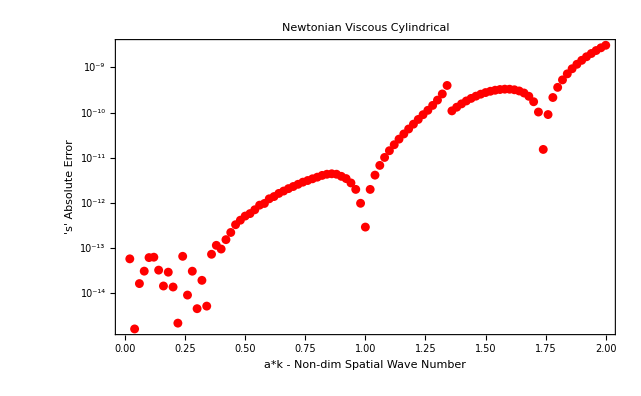

```mathematica
ListLogPlot[Table[{i*2/100,Abs[ys[[i]]-ys2[[i]]]},{i,1,100}],Frame->True,FrameLabel->{"a*k - Non-dim Spatial Wave Number","'s' Absolute Error"},LabelStyle->{FontFamily->"Helvetica",Directive[14]},PlotStyle->{Red,PointSize[0.01]},PlotLabel->"Newtonian Viscous Cylindrical"]
```